# Open Binary Gibbs Energy Library: Unary Reference Reader

## Development exemplar — this notebook is intended to demonstrate the current OBGEL JSON reader and will evolve with the schema and reference implementation.

## Purpose

discussion of purpose to appear here.

## Assumption

Current unary-reader assumption:

All derived unary phase-reference functions share a single
root reference function. The root is the function having no
baseFunction.

Dependencies are resolved symbolically by replacing the
baseFunction identifier with the root reference expression
before constructing Function[{T}, ...] objects.

If future unary data require chained or multiple base-function
dependencies, replace this single-root substitution with a
general dependency-resolution step.

## Setup and data loading

Run this section first. The path is derived from the notebook location so that the exemplar can live inside the repository without hard-coded user-specific paths.

#### Library Location:

```mathematica
ParentDirectory[ParentDirectory[NotebookDirectory[]]]
```

/Users/ccarter/MIT Dropbox/Craig Carter/Projects/open-binary-gibbs-energy-library

```mathematica
obglLibrary = ParentDirectory[ParentDirectory[NotebookDirectory[]]];

If[DirectoryQ[obglLibrary],
$OBGELBaseDirectory = obglLibrary,
Print["OBGEL directory not found: ", obglLibrary]
];
```

#### Loading Data

```mathematica
With[
{
unaryPbJSON =FileNameJoin[{obglLibrary,"data","unary","pb-standard-reference.json"}]
},

Which[
FileExistsQ[unaryPbJSON],
jsonDataUnaryPb = Import[unaryPbJSON, "RawJSON"];
,
True,
StringTemplate["Data files not found:\n `1`"][unaryPbJSON]
]
]
```

Examples of exploring data

```mathematica
Dataset[jsonDataUnaryPb]
```

```mathematica
Dataset[jsonDataUnaryPb["referenceState"]]
```

```mathematica
Dataset[jsonDataUnaryPb["referenceState"]["referenceConditions"]]
```

```mathematica
jsonDataUnaryPb["functions"]//Dataset
```

```mathematica
jsonDataUnaryPb["functions"]["stableReference"]//Dataset
```

```mathematica
jsonDataUnaryPb["functions"]["metastableLiquidReference"]//Dataset
```

```mathematica
jsonDataUnaryPb["functions"]["stableReference"]["temperatureSegments"]//Dataset
```

### Helper Functions

```mathematica
temperatureBasisFunctions = <|
   "constant" -> Function[{T, term}, 1],
   "temperature" -> Function[{T, term}, T],
   "temperatureLogTemperature" -> Function[{T, term}, T Log[T]],
   "temperaturePower" -> Function[{T, term}, T^term["exponent"]]
   |>;

temperatureDependenceExpression[terms_List][T_] :=
    Total[(#["coefficient"] * temperatureBasisFunctions[#["basis"]][T, #]) & /@ terms]

temperatureSegmentExpression[segment_Association][T_] :=
    temperatureDependenceExpression[segment["terms"]][T];
```

Example: Get a list of temperature dependence expressions over the temperature intervals

```mathematica
temperatureSegments = jsonDataUnaryPb["functions"]["stableReference"]["temperatureSegments"];

temperatureSegmentExpression[#][T]&/@temperatureSegments
```

{-7650.09+101.7 T-0.00365895 T^2-2.4395×10^-7 T^3-24.5242 T Log[T],-10531.1+(8.054×10^25)/T^9+154.243 T+0.00154613 T^2-32.4914 T Log[T],4157.62+(8.054×10^25)/T^9-(2.69676×10^6)/T+53.1391 T-0.00288294 T^2+9.8144×10^-8 T^3-18.9641 T Log[T]}

```mathematica
temperatureSegmentsToRanges[T_][temperatureSegment_Association]:= 
Block[{},
Inequality[temperatureSegment["minimumTemperature"],lessOrLessThan[temperatureSegment["minimumInclusive"]],T,lessOrLessThan[temperatureSegment["maximumInclusive"]],temperatureSegment["maximumTemperature"]] 
]
```

Example: Get a list of temperature temperature intervals

```mathematica
temperatureSegmentsToRanges[T]/@temperatureSegments
```

{298.15<T≤600.612,600.612<T≤1200.,1200.<T<2100.}

### Molar free energy extraction functions

```mathematica
Clear[molarGibbsReferenceFunction];
molarGibbsReferenceFunction[json_Association][phaseIdentifier_String]:=
With[{phase= json["functions"][phaseIdentifier]},
Block[
{ functions, ranges, T,temperatureSegments=phase["temperatureSegments"], terms = phase["temperatureSegments"][[All,"terms"]]},
functions =temperatureDependenceExpression[#][T]&/@terms;
ranges = temperatureSegmentsToRanges[T]/@temperatureSegments;
res =Piecewise[Transpose[{functions,ranges}]]+
Which[MissingQ[phase["baseFunction"]],0,True,phase["baseFunction"]]]
]
```

Example: Get the Gibbs energy for the metastable liquid (there may be a place holder for the stable phase which becomes an additive constant

```mathematica
molarGibbsReferenceFunction[jsonDataUnaryPb]["metastableLiquidReference"]
```

gReferencePb+(Piecewise[{{4672.12-7.75068 T-6.019×10^-19 T^7, 298.15<T≤600.612}, {4853.14-(8.054×10^25)/T^9-8.06714 T, 600.612<T<2100.}, {0, True}}])

#### Get a data structure for the molar free energies in the library json.

```mathematica
molarGibbsReference[json_Association]:=
Block[{
functions = json["functions"],
phases,
functionsAssociation,
referencePhase,referenceFunction,referenceFunctionName,referencePhaseKey, result,T,
resultExpressions,resultFunctions
},
phases= Keys[functions];
fa =functionsAssociation =AssociationMap[molarGibbsReferenceFunction[json],phases];
referencePhase=Select[json["functions"],!KeyExistsQ[#,"baseFunction"]&];
referencePhaseKey =Keys[referencePhase][[1]];referenceFunctionName = Values[referencePhase][[1]]["name"];
referenceFunction=functionsAssociation[referencePhaseKey];
re =resultExpressions =functionsAssociation/.referenceFunctionName->referenceFunction;
rf =resultFunctions=Map[Function[{T},#]&,resultExpressions];
AssociateTo[resultFunctions, "stableEnvelope"->Function[{T},Evaluate[Min[Values[resultExpressions]]]]]

(*  renove the stableEnvelope key and construct a stableEnvelope function that takes a list of result and creates the function, i.e.,
stableEnvelope[json][T], thus the stable envelope and stablePhase[molarGibbsReference[json]][T] live outside the association

molarGibbsReference return only the phase-specific unary functions,and that stableEnvelope and stablePhase operate on that returned association.
*)
]
```

Example

```mathematica
examplePbReference=molarGibbsReference[jsonDataUnaryPb]
```

<|stableReference→Function[{T},Piecewise[{{-7650.09+101.7 T-0.00365895 T^2-2.4395×10^-7 T^3-24.5242 T Log[T], 298.15<T≤600.612}, {-10531.1+(8.054×10^25)/T^9+154.243 T+0.00154613 T^2-32.4914 T Log[T], 600.612<T≤1200.}, {4157.62+(8.054×10^25)/T^9-(2.69676×10^6)/T+53.1391 T-0.00288294 T^2+9.8144×10^-8 T^3-18.9641 T Log[T], 1200.<T<2100.}, {0, True}}]],metastableLiquidReference→Function[{T},(Piecewise[{{4672.12-7.75068 T-6.019×10^-19 T^7, 298.15<T≤600.612}, {4853.14-(8.054×10^25)/T^9-8.06714 T, 600.612<T<2100.}, {0, True}}])+(Piecewise[{{-7650.09+101.7 T-0.00365895 T^2-2.4395×10^-7 T^3-24.5242 T Log[T], 298.15<T≤600.612}, {-10531.1+(8.054×10^25)/T^9+154.243 T+0.00154613 T^2-32.4914 T Log[T], 600.612<T≤1200.}, {4157.62+(8.054×10^25)/T^9-(2.69676×10^6)/T+53.1391 T-0.00288294 T^2+9.8144×10^-8 T^3-18.9641 T Log[T], 1200.<T<2100.}, {0, True}}])],stableEnvelope→Function[{T},Min[Piecewise[{{-7650.09+101.7 T-0.00365895 T^2-2.4395×10^-7 T^3-24.5242 T Log[T], 298.15<T≤600.612}, {-10531.1+(8.054×10^25)/T^9+154.243 T+0.00154613 T^2-32.4914 T Log[T], 600.612<T≤1200.}, {4157.62+(8.054×10^25)/T^9-(2.69676×10^6)/T+53.1391 T-0.00288294 T^2+9.8144×10^-8 T^3-18.9641 T Log[T], 1200.<T<2100.}, {0, True}}],(Piecewise[{{4672.12-7.75068 T-6.019×10^-19 T^7, 298.15<T≤600.612}, {4853.14-(8.054×10^25)/T^9-8.06714 T, 600.612<T<2100.}, {0, True}}])+(Piecewise[{{-7650.09+101.7 T-0.00365895 T^2-2.4395×10^-7 T^3-24.5242 T Log[T], 298.15<T≤600.612}, {-10531.1+(8.054×10^25)/T^9+154.243 T+0.00154613 T^2-32.4914 T Log[T], 600.612<T≤1200.}, {4157.62+(8.054×10^25)/T^9-(2.69676×10^6)/T+53.1391 T-0.00288294 T^2+9.8144×10^-8 T^3-18.9641 T Log[T], 1200.<T<2100.}, {0, True}}])]]|>

### visual debugging

```mathematica
examplePbReference["stableReference"]
```

Function[{T},Piecewise[{{-7650.09+101.7 T-0.00365895 T^2-2.4395×10^-7 T^3-24.5242 T Log[T], 298.15<T≤600.612}, {-10531.1+(8.054×10^25)/T^9+154.243 T+0.00154613 T^2-32.4914 T Log[T], 600.612<T≤1200.}, {4157.62+(8.054×10^25)/T^9-(2.69676×10^6)/T+53.1391 T-0.00288294 T^2+9.8144×10^-8 T^3-18.9641 T Log[T], 1200.<T<2100.}, {0, True}}]]

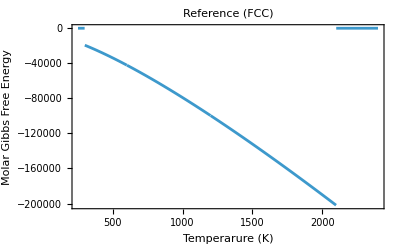

```mathematica
Plot[examplePbReference["stableReference"][temperature],{temperature,250,2400},
Frame->True,FrameLabel->{"Temperarure (K)","Molar Gibbs Free Energy"}, PlotLabel->"Reference (FCC)"]
```

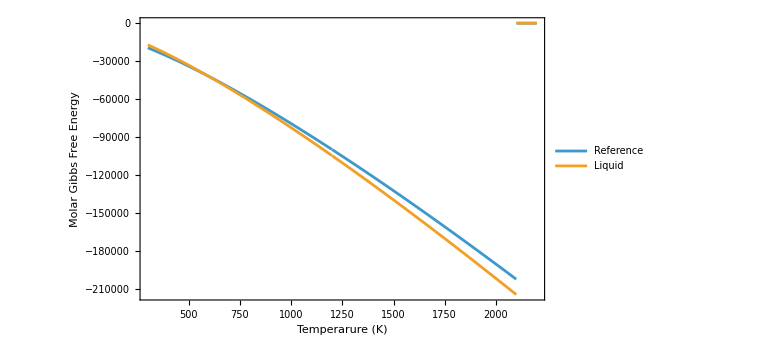

```mathematica
Plot[{examplePbReference["stableReference"][temperature],examplePbReference["metastableLiquidReference"][temperature]},{temperature,300,2200}, Frame->True,FrameLabel->{"Temperarure (K)","Molar Gibbs Free Energy"}, PlotLegends->{"Reference", "Liquid"},ImageSize->Large]
```

Find the transition temperature:

```mathematica
transitionTemperature = temperature/.FindRoot[examplePbReference["stableReference"][temperature]==  examplePbReference["metastableLiquidReference"][temperature], {temperature,300}]
```

600.612

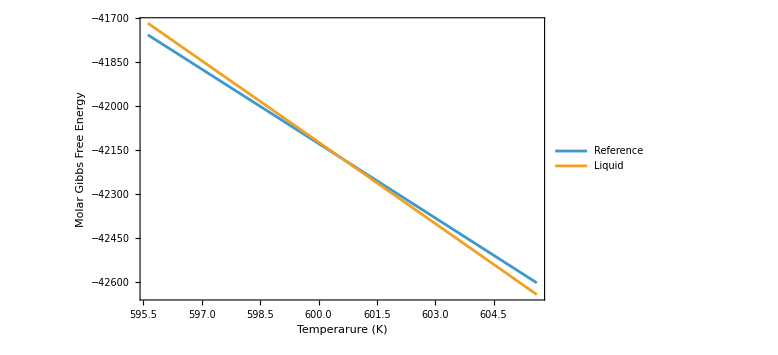

```mathematica
Plot[{examplePbReference["stableReference"][temperature],examplePbReference["metastableLiquidReference"][temperature]},{temperature,transitionTemperature-5,transitionTemperature+5}, Frame->True,FrameLabel->{"Temperarure (K)","Molar Gibbs Free Energy"}, PlotLegends->{"Reference", "Liquid"},ImageSize->Large]
```

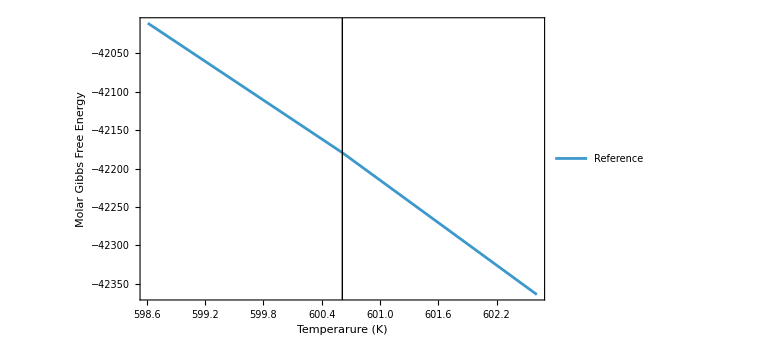

```mathematica
Plot[examplePbReference["stableEnvelope"][temperature],{temperature,transitionTemperature-2,transitionTemperature+2}, Frame->True,FrameLabel->{"Temperarure (K)","Molar Gibbs Free Energy"}, PlotLegends->{"Reference", "Liquid"},ImageSize->Large, Epilog->{InfiniteLine[{transitionTemperature,0},{0,1}]}]
```

## Example for Bi

```mathematica
With[
{
unaryBiJSON =FileNameJoin[{obglLibrary,"data","unary","bi-standard-reference.json"}]
},

Which[
FileExistsQ[unaryBiJSON],
jsonDataUnaryBi = Import[unaryBiJSON, "RawJSON"];
,
True,
StringTemplate["Data files not found:\n `1`"][unaryBiJSON]
]
]
```

```mathematica
Dataset[jsonDataUnaryBi]
```

```mathematica
Dataset[jsonDataUnaryBi["functions"]]
```

```mathematica
Dataset[
exampleBiReference=molarGibbsReference[jsonDataUnaryBi]
]
```

```mathematica
Keys[exampleBiReference]
```

{stableReference,metastableLiquidReference,metastableFccReference,metastableHcpReference,stableEnvelope}

```mathematica
tmp =KeyDrop[exampleBiReference,"stableEnvelope"];
```

```mathematica
funcs = Values[KeyDrop[exampleBiReference,"stableEnvelope"]]
```

{Function[{T},Piecewise[{{-7817.78+128.419 T+0.0123389 T^2-8.3816×10^-6 T^3-28.4097 T Log[T], 298.15<T≤544.55}, {30208.+(1.66145×10^25)/T^9-(3.61617×10^6)/T-393.65 T-0.0753112 T^2+0.0000134999 T^3+51.8557 T Log[T], 544.55<T≤800.}, {-11045.7+(1.66145×10^25)/T^9+182.549 T+0.0074266 T^2-1.046×10^-6 T^3-35.9824 T Log[T], 800.<T≤1200.}, {-7581.31+(1.66145×10^25)/T^9+124.771 T-27.196 T Log[T], 1200.<T<3000.}, {0, True}}]],Function[{T},(Piecewise[{{11245.9-20.6374 T-5.9726×10^-19 T^7, 298.15<T≤544.52}, {11336.4-(1.66491×10^25)/T^9-20.8117 T, 544.52<T<3000.}, {0, True}}])+(Piecewise[{{-7817.78+128.419 T+0.0123389 T^2-8.3816×10^-6 T^3-28.4097 T Log[T], 298.15<T≤544.55}, {30208.+(1.66145×10^25)/T^9-(3.61617×10^6)/T-393.65 T-0.0753112 T^2+0.0000134999 T^3+51.8557 T Log[T], 544.55<T≤800.}, {-11045.7+(1.66145×10^25)/T^9+182.549 T+0.0074266 T^2-1.046×10^-6 T^3-35.9824 T Log[T], 800.<T≤1200.}, {-7581.31+(1.66145×10^25)/T^9+124.771 T-27.196 T Log[T], 1200.<T<3000.}, {0, True}}])],Function[{T},(Piecewise[{{9900.-12.5 T, 298.15<T<3000.}, {0, True}}])+(Piecewise[{{-7817.78+128.419 T+0.0123389 T^2-8.3816×10^-6 T^3-28.4097 T Log[T], 298.15<T≤544.55}, {30208.+(1.66145×10^25)/T^9-(3.61617×10^6)/T-393.65 T-0.0753112 T^2+0.0000134999 T^3+51.8557 T Log[T], 544.55<T≤800.}, {-11045.7+(1.66145×10^25)/T^9+182.549 T+0.0074266 T^2-1.046×10^-6 T^3-35.9824 T Log[T], 800.<T≤1200.}, {-7581.31+(1.66145×10^25)/T^9+124.771 T-27.196 T Log[T], 1200.<T<3000.}, {0, True}}])],Function[{T},(Piecewise[{{9900.-11.8 T, 298.15<T<3000.}, {0, True}}])+(Piecewise[{{-7817.78+128.419 T+0.0123389 T^2-8.3816×10^-6 T^3-28.4097 T Log[T], 298.15<T≤544.55}, {30208.+(1.66145×10^25)/T^9-(3.61617×10^6)/T-393.65 T-0.0753112 T^2+0.0000134999 T^3+51.8557 T Log[T], 544.55<T≤800.}, {-11045.7+(1.66145×10^25)/T^9+182.549 T+0.0074266 T^2-1.046×10^-6 T^3-35.9824 T Log[T], 800.<T≤1200.}, {-7581.31+(1.66145×10^25)/T^9+124.771 T-27.196 T Log[T], 1200.<T<3000.}, {0, True}}])]}

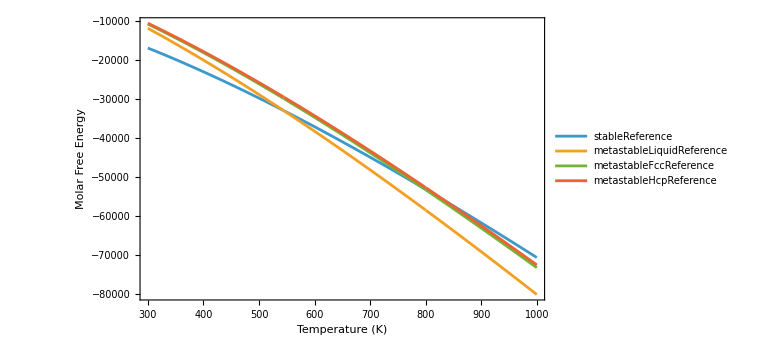

```mathematica
With[{funcs =Comap[Values[KeyDrop[exampleBiReference,"stableEnvelope"]], temperature]},
 Plot[funcs,{temperature,300,1000}, PlotLegends->Keys[KeyDrop[exampleBiReference,"stableEnvelope"]],
Frame->True, FrameLabel->{"Temperature (K)", "Molar Free Energy"}, ImageSize->Large]
]
```

```mathematica
Keys[exampleBiReference]
```

{stableReference,metastableLiquidReference,metastableFccReference,metastableHcpReference,stableEnvelope}

```mathematica
FindRoot[exampleBiReference["stableReference"][T]== exampleBiReference["metastableLiquidReference"][T],{T,500}]
```

{T→544.52}

```mathematica
544.5200027063481
```

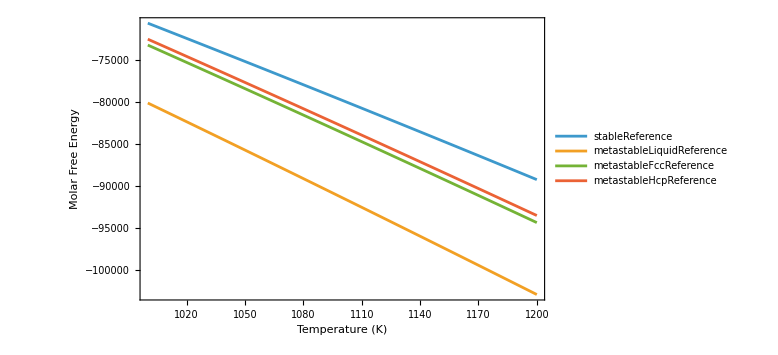

```mathematica
With[{funcs =Comap[Values[KeyDrop[exampleBiReference,"stableEnvelope"]], temperature]},
 Plot[funcs,{temperature,1000,1200}, PlotLegends->Keys[KeyDrop[exampleBiReference,"stableEnvelope"]],
Frame->True, FrameLabel->{"Temperature (K)", "Molar Free Energy"}, ImageSize->Large]
]
```